# Лабораторная работа 13. Компьютерные модели аналитической геометрии. Геометрический объект “прямая на плоскости”

Выполнила студентка ММФ БГУ
 1 к, 5 гр. Шклярик В.С.
 1 декабря 2021

```mathematica
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
kmPoint[{ϕ_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[ϕ],ρ Sin[ϕ]}];
kmPoint[id_String,{ϕ_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}];
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
ClearAll[kmPointShow];
kmPointShow[gp_List,color_:Black,opts___]:=Graphics[{ReplaceAll[gp,P_kmPoint:>{color,AbsolutePointSize[5],Tooltip[Point@P@"coord",{P/@{"id","coord"},TreeForm@P}]}]},opts];
```

```mathematica
ClearAll[kmVector];
NamedQ[kmVector[km,id_String,___]]^:=id≠"";
kmVector[id_String,coord_List]:=kmVector[km, id,coord ];
kmVector[coord_List]:=kmVector["",coord];
kmVector[id_String,p0_kmPoint,p1_kmPoint]:=kmVector[id,p1["coord"]-p0["coord"]];
kmVector[p0_kmPoint,p1_kmPoint]:=kmVector[If[And@@NamedQ/@{p0,p1},StringJoin[p0@"id",p1@"id"],""],p0,p1];
kmVector[id_String,ort:{_,_},length_]:=kmVector[id,ort*length];
kmVector[ort:{_,_},length_]:=kmVector["",ort*length];
kmVector[km,id_String,___]["id"]:=If[id=="","Вектор",id];
kmVector[km,id_String,coord_List,___]["coord"]:=coord;
kmVector[km,id_String,coord_List,___]["length"]:=√(#.#)&[kmVector[id,coord]["coord"]];
kmVector[km,id_String,coord_List,___]["ort"]:=kmVector["ort",(kmVector[id,coord]["coord"])/(kmVector[id,coord]["length"])];
```

## Задание 1.

Внутреннее представление объекта «прямая на плоскости» 
{A, B, C} – список, содержащий коэффициенты-параметры общего уравнения прямой Ax +By + C = 0

```mathematica
kmLine[km,id_String,{A_,B_,C_}]
```

kmLine[km,id_String,{A_,B_,C_}]

## Задание 2.

Булева функция NamedQ, позволяющая определить, имеет ли объект “прямая” имя.

```mathematica
NamedQ[kmLine[km,id_String,___]]^:=id≠"";
```

Тест функции

```mathematica
NamedQ[kmLine[km,"test",{1,2,-3}]]
```

True

```mathematica
NamedQ[L]
```

NamedQ[L]

## Задание 4.

Конструктор для построения прямой по ее имени и общему уравнению.
На входе: имя прямой, общее уравнение прямой , список имен переменных в общем уравнении.

```mathematica
kmLine[id_String,A_. x_+B_. y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[km,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B]
```

```mathematica
ClearAll[a];
kmLine["L1",5 f-a==0,{f,a}]
```

kmLine[km,L1,{5,-1,0}]

```mathematica
kmLine["L1",5 f-a==0,{a,f}]
```

kmLine[km,L1,{-1,5,0}]

```mathematica
kmLine["L2",5 f==0,{f,a}]
```

kmLine[L2,5 f==0,{f,a}]

```mathematica
MatchQ[5 f==0,A_. x_+B_. y_+C_.==0]
```

False

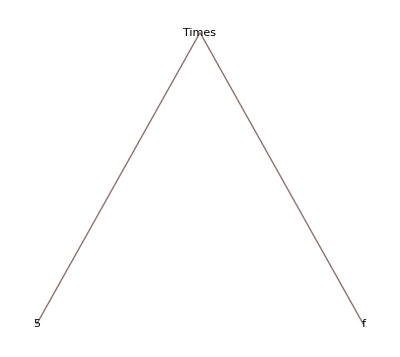

```mathematica
TreeForm[5 f]
```

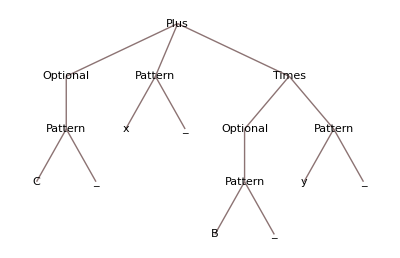

```mathematica
TreeForm[x_+B_. y_+C_.]
```

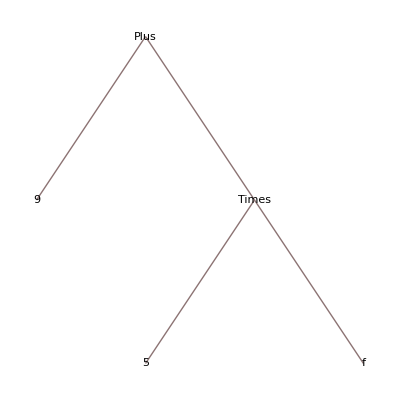

```mathematica
TreeForm[5 f+9]
```

```mathematica
MatchQ[5 f+9==0,A_. x_+B_. y_+C_.==0]
```

True

Уравнение соответствует образцу, т. к. совпадает структура выражений.

```mathematica
kmLine["L3",5 f+9==0,{f,a}]
```

kmLine[L3,9+5 f==0,{f,a}]

```mathematica
kmLine["L2",5 f+7==0,{f,a}]
```

kmLine[L2,7+5 f==0,{f,a}]

```mathematica
MatchQ[{id_String,A_. x_+B_. y_+C_.==0,{x_Symbol,y_Symbol}},{5 f+7==0,{f,a}}]//Trace
```

{{{{A_. x_+B_. y_+C_.,C_.+A_. x_+B_. y_},C_.+A_. x_+B_. y_==0},{id_String,C_.+A_. x_+B_. y_==0,{x_Symbol,y_Symbol}}},{{{5 f+7,7+5 f},7+5 f==0},{7+5 f==0,{f,a}}},MatchQ[{id_String,C_.+A_. x_+B_. y_==0,{x_Symbol,y_Symbol}},{7+5 f==0,{f,a}}],False}

т.к из-за Optional B представляется системе как 1, то а определяется как 7, а 7 не имеет головы Symbol, поэтому выражение не совпадает с образцом.

```mathematica
kmLine[id_String,A_. x_+C_.==0,{x_Symbol,_Symbol}]:=kmLine[km,id,{A,0,C}];
kmLine[id_String,B_. y_+C_.==0,{_Symbol,y_Symbol}]:=kmLine[km,id,{0,B,C}];
```

Именован только один элемент списка переменных, !!!!!!!!!!!!!!!!

```mathematica
kmLine["L2",5 f+7==0,{f,a}]
```

kmLine[km,L2,{5,0,7}]

```mathematica
kmLine["L2",5 f==0,{f,a}]
```

kmLine[km,L2,{5,0,0}]

```mathematica
kmLine["L2",5 f==0,{a,f}]
```

kmLine[km,L2,{0,5,0}]

```mathematica
kmLine["L3",5==0,{f,a}]
```

kmLine[L3,False,{f,a}]

```mathematica
kmLine[km,"",{A_,B_,_}]:=Abort[]/;PossibleZeroQ[Abs@A+Abs@B]
```

Чтобы предотвратить ошибочное представление прямой, указываем, что необходимо прекратить вычисления в случае нулевых A, B.

```mathematica
kmLine[km,"",{0,0.,3}]
```

$Aborted

## Задание 5

Конструктор, строящий  объект “прямая”  по общему уравнению и списку переменных. Сводим конструктор к первому базовому.

```mathematica
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars]
```

```mathematica
kmLine[5 f+3==0,{f,a}]
```

kmLine[km,,{5,0,3}]

## Задание 6

### Способ 1

Заключается в построении общего уравнения прямой по точке(объект “точка”) и направляющему вектору(объект “вектор”).

```mathematica
{P,P0}=kmPoint/@{{x,y},{p0x,p0y}}
```

{kmPoint[km,,{x,y}],kmPoint[km,,{p0x,p0y}]}

```mathematica
V=kmVector[{Vx,Vy}]
```

kmVector[km,,{Vx,Vy}]

```mathematica
{V@"coord",P@"coord"-P0@"coord"}//MatrixForm
```

(Vx | Vy
-p0x+x | -p0y+y)

```mathematica
Det[{V@"coord",P@"coord"-P0@"coord"}]==0
```

-p0y Vx+p0x Vy-Vy x+Vx y==0

Конструктор, строящий  объект “прямая”  по точке (объект “точка”) и направляющему вектору (объект “вектор”) с указанием имени прямой.

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[id,Det[{Dir@"coord",{x,y}-P0@"coord"}]==0,{x,y}]
```

```mathematica
kmLine["L",kmPoint[{5,5}],kmVector[{-1,1}]]
```

kmLine[km,L,{-1,-1,10}]

### Способ 2

Заключается в вычислении коэффициентов общего уравнения прямой.

```mathematica
({{0, -1}, {1, 0}}).V@"coord"
```

{-Vy,Vx}

Нормаль, где -Vy = А, Vx = В.

```mathematica
-(({{0, -1}, {1, 0}}).V@"coord").P0@"coord"
```

-p0y Vx+p0x Vy

Вычисление параметра С.

```mathematica
Append[#,-#.P0["coord"]]&[({{0, -1}, {1, 0}}).V@"coord"]
```

{-Vy,Vx,-p0y Vx+p0x Vy}

Готовый список {A,B,C}.

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[km,id,Append[#,-#.P0["coord"]]&[({{0, -1}, {1, 0}}).Dir@"coord"]]
```

```mathematica
kmLine["",P0,V]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
kmLine["",kmPoint[{2,3}],kmVector[{10,20}]]
```

kmLine[km,,{-20,10,10}]

Конструктор для построения  объекта “прямая”  по точке и направляющему вектор без указания имени прямой.

```mathematica
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[If[And@@(NamedQ/@{P,Dir}),StringJoin[P@"id",Dir@"id"],""],P,Dir]
```

```mathematica
kmLine[P0,V]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
P1=kmPoint["A",{Ax,Ay}]
```

kmPoint[km,A,{Ax,Ay}]

```mathematica
a=kmVector["a",{ax,ay}]
```

kmVector[km,a,{ax,ay}]

```mathematica
kmLine[P1,a]
```

kmLine[km,Aa,{-ay,ax,Ax ay-ax Ay}]

## Задание 7.

Конструкторы для построения объекта “прямая” по двум различным точкам (объектам “точка”), ей принадлежащим в случаях,  если прямая либо именована, либо нет.

```mathematica
kmLine[id_String,P1_kmPoint,P2_kmPoint]:=kmLine[id,P1,kmVector[P1,P2]];
```

```mathematica
kmLine[P1_kmPoint,P2_kmPoint]:=kmLine["",P1,kmVector[P1,P2]];
```

Тест конструкторов

```mathematica
kmLine["LL",kmPoint[{2,3}],kmPoint[{10,20}]]
```

kmLine[km,LL,{-17,8,10}]

```mathematica
kmLine[kmPoint[{7,5}],kmPoint[{2,10}]]
```

kmLine[km,,{-5,-5,60}]

## Задание 8.

Функция showNormal отображает заданный вектор, его левую и правую нормали.

```mathematica
ClearAll[showNormal];
showNormal[vect_kmVector]:=Module[{coord=vect["coord"]},Graphics[MapThread[Tooltip,{Line[{{0,0},#1}]&/@{
coord,{-coord⟦2⟧,coord⟦1⟧},{coord⟦2⟧,-coord⟦1⟧}},{"V","N_L","N_R"}}],Axes->True]]
```

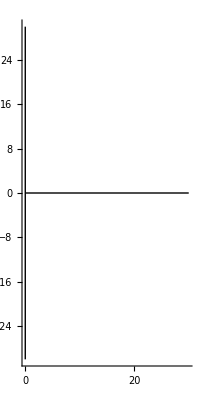

```mathematica
showNormal[kmVector[{6,9},{5,0}]]
```

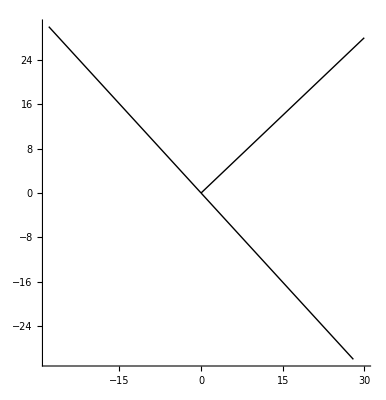

```mathematica
showNormal[kmVector[{6,7},{5,4}]]
```

## Задание 9.

```mathematica
V=kmVector[{Vx,Vy}]
```

kmVector[km,,{Vx,Vy}]

Функция Nleft строит для заданного вектора лево ориентированную нормаль(так же объект “вектор”).

```mathematica
Nleft[vect_kmVector]:=kmVector[({{0, -1}, {1, 0}}).vect@"coord"]
```

```mathematica
Nleft[V]
```

kmVector[km,,{-Vy,Vx}]

## Задание 10.

Функция vectDir строит направляющий вектор прямой, если задана лево ориентированная нормаль(объект “вектор”) к этой прямой.

```mathematica
vectDir[Nleft_kmVector]:=kmVector[({{0, 1}, {-1, 0}}).Nleft@"coord"]
```

```mathematica
vectDir[V]
```

kmVector[km,,{Vy,-Vx}]

## Задание 11.

Конструкторы для построения объекта “прямая” по заданной точке, ей принадлежащей, и нормальному вектору к этой прямой. Прямая может быть именована, либо нет. 
На входе: объект “точка”(точка прямой), объект “вектор” (нормаль к прямой),  дополнительный аргумент “normal”, указывающий способ задания прямой.

```mathematica
kmLine[id_String,P0_kmPoint,normal_kmVector,"normal"]:=kmLine[id,P0,vectDir[normal]]
```

```mathematica
kmLine["test",kmPoint[{1,1}],kmVector[{1,1},{1,2}],"normal"]
```

kmLine[km,test,{1,2,-3}]

```mathematica
kmLine[P0_kmPoint,normal_kmVector,"normal"]:=kmLine["",P0,vectDir[normal]]
```

## Задание 12.

Оператор, возвращающий имя объекта “прямая”, если оно существует, и имя “Прямая” в противном случае.

```mathematica
kmLine[km,id_String,___]["id"]:=If[id=="","Прямая",id];
```

Тест оператора

```mathematica
kmLine[km,"test",{1,2,-3}]["id"]
```

test

```mathematica
kmLine[kmPoint[{9,8}],kmPoint[{2,4}]]["id"]
```

Прямая

## Задание 13.

Оператор, возвращающий список
коэффициентов общего уравнения прямой.

```mathematica
kmLine[km,___,{A_,B_,C_}]["coef"]:={A,B,C}
```

Тест оператора

```mathematica
kmLine[km,"test",{1,2,-3}]["coef"]
```

{1,2,-3}

```mathematica
kmLine[kmPoint[{9,8}],kmPoint[{2,4}]]["coef"]
```

{4,-7,20}

## Задание 14.

Оператор, возвращающий общее уравнение 
прямой.

```mathematica
kmLine[km,___,{A_,B_,C_}]["equ"]:=A x +B y+C==0
```

Тест оператора

```mathematica
kmLine[km,"test",{1,2,-3}]["equ"]
```

-3+x+2 y==0

```mathematica
kmLine[kmPoint[{9,8}],kmPoint[{2,4}]]["equ"]
```

20+4 x-7 y==0

```mathematica
kmLine[3x+5==0,{x,y}]["equ"]
```

5+3 x==0

```mathematica
kmLine[3x+5==0,{x,y}]["coef"]
```

{3,0,5}

## Задание 15.

Оператор, возвращающий нормальный 
вектор прямой.

```mathematica
kmLine[km,___,{A_,B_,_}]["norm"]:=kmVector[{A,B}]
```

```mathematica
kmLine[3x+5==0,{x,y}]["norm"]
```

kmVector[km,,{3,0}]

## Задание 16.

Оператор, возвращающий направляющий 
вектор прямой.

```mathematica
kmLine[km,___,{A_,B_,_}]["dir"]:=kmVector[{-B,A}]
```

```mathematica
L["dir"]
```

kmVector[km,,{8,17}]

## Задание 17.

```mathematica
L=kmLine[km,"",{17,-8,-10}]
```

kmLine[km,,{17,-8,-10}]

```mathematica
L@"coef".{x0,y,1}==0
```

-10-8 y+17 x0==0

```mathematica
First@Solve[L@"coef".{x0,y,1}==0,y]
```

{y→1/8 (-10+17 x0)}

```mathematica
{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0,y]
```

{x0,1/8 (-10+17 x0)}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0,y],{x0,{-1,1}}]
```

{{-1,-27/8},{1,7/8}}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0],{x0,{-1,1}}]
```

{{-1,-27/8},{1,7/8}}

```mathematica
Ly=kmLine[km,"",{0,-8,-10}]
```

kmLine[km,,{0,-8,-10}]

```mathematica
Table[{x0,y}/.First@Solve[Ly@"coef".{x0,y,1}==0],{x0,{-1,1}}]
```

{{-1,-5/4},{1,-5/4}}

```mathematica
Lx=kmLine[km,"",{17,0,-10}]
```

kmLine[km,,{17,0,-10}]

```mathematica
Lx@"coef".{1,y,1}==0
```

False

```mathematica
If[Apply[Less,Abs@L["coef"]⟦{1,2}⟧],Table[{x0,y}/.First@Solve[L["coef"].{x0,y,1}==0],{x0,{-1,1}}],Table[{x,y0}/.First@Solve[L["coef"].{x,y0,1}==0],{y0,{-1,1}}]]
```

{{2/17,-1},{18/17,1}}

Функция kmGetTwoLinePoints для заданного объекта “прямая” возвращает два объекта “точка”, эти точки принадлежат заданной прямой.

```mathematica
ClearAll[kmGetTwoLinePoints];
kmGetTwoLinePoints[line_kmLine]:=Map[kmPoint,If[Apply[Less,Abs@line["coef"]⟦{1,2}⟧],Table[{x,y}/.First@Solve[line["coef"].{x,y,1}==0],{x,{-1,1}}],Table[{x,y}/.First@Solve[line["coef"].{x,y,1}==0],{y,{-1,1}}]]]
```

```mathematica
kmGetTwoLinePoints/@{L,Ly,Lx}
```

{{kmPoint[km,,{2/17,-1}],kmPoint[km,,{18/17,1}]},{kmPoint[km,,{-1,-5/4}],kmPoint[km,,{1,-5/4}]},{kmPoint[km,,{10/17,-1}],kmPoint[km,,{10/17,1}]}}

## Задание 18.

Функция kmGraphics2D отображает заданные объекты “точка” и “прямая”.

```mathematica
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[ReplaceAll[gp,{P_kmPoint:>Tooltip[Point@P@"coord",Style[Format[P,StandardForm],Large]],L_kmLine:>Tooltip[InfiniteLine@Through@kmGetTwoLinePoints[L]@"coord",Style[Format[L,StandardForm],Large]]}],opts]
```

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
{L1,L2}=kmLine[km,"",#]&/@{{1,5,3},{-2,3,-1}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

{kmLine[km,,{1,5,3}],kmLine[km,,{-2,3,-1}]}

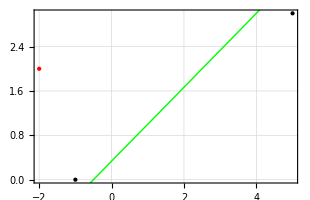

```mathematica
kmGraphics2D[{{PointSize@Large,P1,P2,Red,P3},{Thick,Blue,L1,Green,L2}},Frame->True,GridLines->Automatic,PlotRange->All]
```